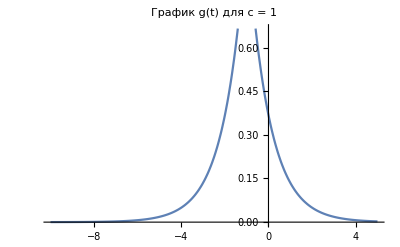
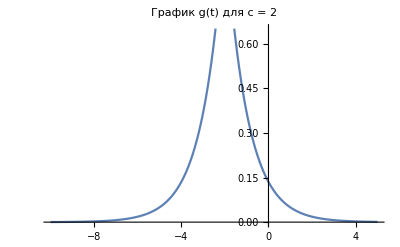
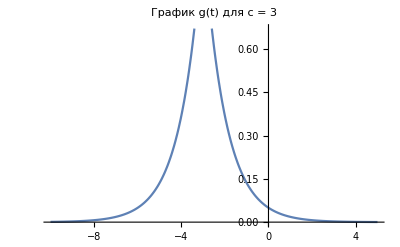

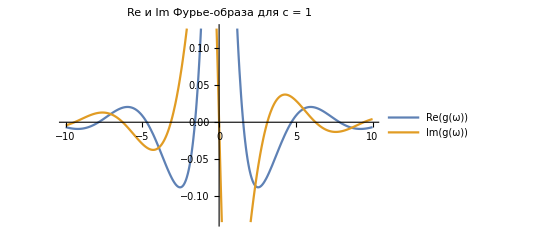
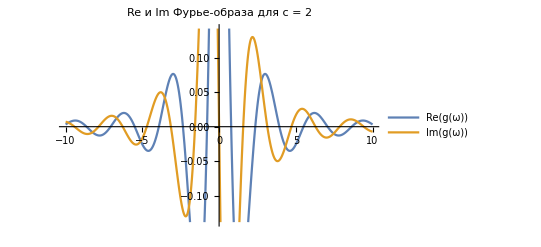
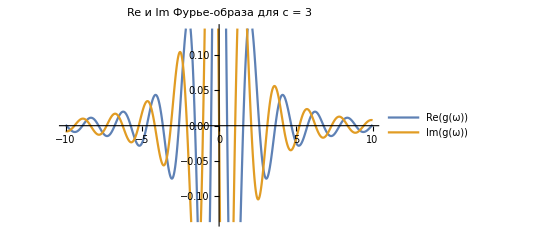

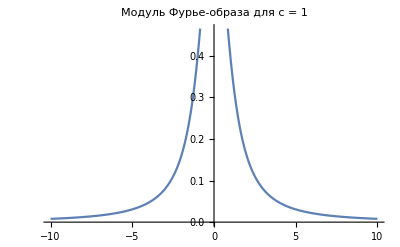
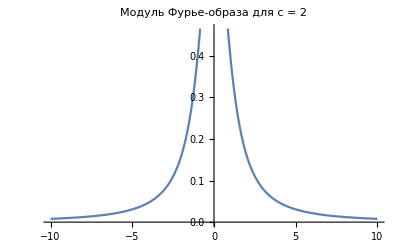

```mathematica
a=1;
b=1;
f[t_]:=a Exp[-b Abs[t]];

cValues={1,2,3};
g[t_,c_]:=f[t+c];

fourierTransforms=Table[FourierTransform[g[t,c],t,ω],{c,cValues}];

plotsG=Table[Plot[g[t,c],{t,-10,5},PlotLabel->"График g(t) для c = "<>ToString[c]],{c,cValues}]

plotsReIm=Table[Plot[{Re[fourierTransforms[[c]]],Im[fourierTransforms[[c]]]},{ω,-10,10},PlotLegends->{"Re(g(ω))","Im(g(ω))"},PlotLabel->"Re и Im Фурье-образа для c = "<>ToString[cValues[[c]]]],{c,Length[cValues]}]

plotsAbs=Table[Plot[Abs[fourierTransforms[[c]]],{ω,-10,10},PlotLabel->"Модуль Фурье-образа для c = "<>ToString[cValues[[c]]]],{c,Length[cValues]}]
```